```mathematica
<<7primegraphsource.m
```

LinkObject::linkw: Unable to write data to closed link ….

General::stop: Further output of LinkObject::linkw will be suppressed during this calculation.

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,133,9].

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,134,10].

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,135,11].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Parallel`Developer`ConnectKernel::failinit: 4 of 4 kernels failed to initialize.

ParallelCombine::nopar: No parallel kernels available; proceeding with sequential evaluation.

Select::normal: Nonatomic expression expected at position 1 in Select[primegraphs,maximalQ].

AdjacencyGraph::matsq: Argument primegraphs at position 1 is not a non-empty square matrix.

AdjacencyGraph::matsq: Argument maximalQ at position 1 is not a non-empty square matrix.

AdjacencyGraph::argt: AdjacencyGraph called with 0 arguments; 1 or 2 arguments are expected.

Part::partw: Part 1 of {} does not exist.

Part::take: Cannot take positions 2 through 4 in {Null,{}}⟦2,1⟧.

AdjacencyGraph::matsq: Argument primegraphs at position 1 is not a non-empty square matrix.

General::stop: Further output of AdjacencyGraph::matsq will be suppressed during this calculation.

GraphComplement::graph: A graph object is expected at position 1 in GraphComplement[AdjacencyGraph[primegraphs]].

{}

```mathematica
maximalQ[mat1_]:=Module[{t,mat2},t=True;
Do[If[i≠j&&mat1[[i,j]]==0,mat2=mat1;
mat2[[i,j]]=1;
mat2[[j,i]]=1;
If[MemberQ[primegraphs,mat2],t=False;
Break[]]],{i,Length[mat1]},{j,i,Length[mat1]}];
Return[t(*{t,AdjacencyGraph[mat2],MatrixForm[mat2-mat1]}*)];];
primeGraphQ[mat1_]:=Module[{t,mat2},t=False;
mat2=MatrixPower[mat1,3];
If[ContainsOnly[Table[mat2[[k,k]],{k,Length[mat1]}],{0}],If[ChromaticPolynomial[AdjacencyGraph[mat1],3]≠0,t=True;]];
Return[t];];
findAllGraphs[mat1_,starti_,startj_]:=Module[{mat2,i,j},i=starti;
j=startj;
If[i==Length[mat1]&&j>Length[mat1],If[primeGraphQ[mat1],Sow[mat1];],If[j>Length[mat1],i=i+1;
j=i;];
findAllGraphs[mat1,i,j+1];
If[i≠j,mat2=mat1;
mat2[[i,j]]=1;
mat2[[j,i]]=1;
(*Echo[mat2];*)findAllGraphs[mat2,i,j+1];];]];
$RecursionLimit=10000
(*Get["7primegraphs.m"]*)
AbsoluteTiming[primegraphs=Reap[findAllGraphs[ConstantArray[0,{7,7}],1,1]][[2,1]];]
```

10000

{595.014,Null}

```mathematica
Dimensions[primegraphs]
```

{133501,7,7}

```mathematica
maximalprimegraphs=Parallelize[Select[primegraphs,maximalQ]];
```

ParallelCombine::nopar: No parallel kernels available; proceeding with sequential evaluation.

$Aborted

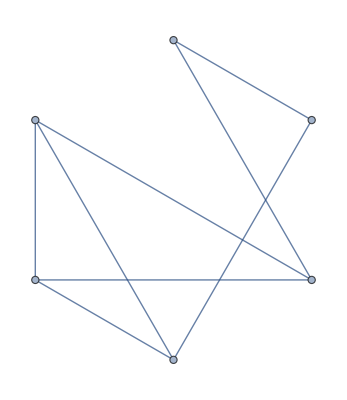

```mathematica
isomaxprimegraphs=AdjacencyGraph/@maximalprimegraphs;
isomaxprimegraphs=Tuples[{isomaxprimegraphs,isomaxprimegraphs}];
isomaxprimegraphsbool=Reap[Do[Sow[IsomorphicGraphQ[isomaxprimegraphs[[i,1]],isomaxprimegraphs[[i,2]]]],{i,Length[isomaxprimegraphs]}]][[2,1]];
isomaxgraphs=Reap[Do[If[Apply[BooleanCountingFunction[1,i],isomaxprimegraphsbool[[i;;((i-1)*Length[maximalprimegraphs]+i);;Length[maximalprimegraphs]]]],Sow[maximalprimegraphs[[i]]]],{i,Length[maximalprimegraphs]}]][[2,1]];
minimalPrimeGraphs=GraphComplement/@AdjacencyGraph/@Select[isomaxgraphs,ConnectedGraphQ[GraphComplement[AdjacencyGraph[#]]]&];
minimalPrimeGraphs
```

```mathematica
Beep[]
```